## List of US Presidents Data from Wikipedia

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/DataVisualization/Other/us-presidents

```mathematica
listOfPresidents=Import["list-of-us-presidents.csv"];
```

```mathematica
listOfPresidents[[1]]//MatrixForm
```

(President
Years in office
Year first inaugurated
Age at inauguration
State elected from
# of electoral votes
 # of popular votes 
 National total votes 
Total electoral votes
Rating points
Political Party
Occupation
College
% electoral
% popular)

Define a function that generates Histograms

```mathematica
histo[list_,column_,title_,imagesize_:Large]:=Module[{listM},

listM=Sort[(Transpose@list)[[column]][[2;;]]];
BarChart[Counts@listM,ChartLabels->Automatic,ImageSize->imagesize,Frame->True,PlotLabel->title,ChartStyle->Gray,ChartBaseStyle->EdgeForm[None]]
]
```

Another way of making the histograms

```mathematica
histo2[list_,column_,title_,imagesize_:Large,angle_:0]:=Module[{listM,listM2,nonePosM},

listM=Sort[
Tally[(Transpose@list)[[column]][[2;;]]]
];
listM2=Transpose[listM];
nonePosM=Position;

BarChart[listM2[[2]],
ChartLabels->Placed[listM2[[1]],Axis,Rotate[#,angle]&],
Frame->True,ImageSize->imagesize,PlotLabel->title,
ChartStyle->Gray,ChartBaseStyle->EdgeForm[None]]
];
```

```mathematica
(* histo3 move the None element to the end of the list *)
histo3[list_,column_,title_,imagesize_:Large,angle_:0]:=Module[{listM,listM2,nonePosM,dataM,labelM},

listM=Sort[
Tally[(Transpose@list)[[column]][[2;;]]]
];
nonePosM=Position[listM,"None"][[1,1]];

listM2=Transpose[
Append[Delete[listM,nonePosM],listM[[nonePosM]]]
];


BarChart[
listM2[[2]],
ChartLabels->Placed[listM2[[1]],Axis,Rotate[#,angle]&],
Frame->True,ImageSize->imagesize,PlotLabel->title,
ChartStyle->Gray,ChartBaseStyle->EdgeForm[None]]


]
```

Which Parties Are They From?

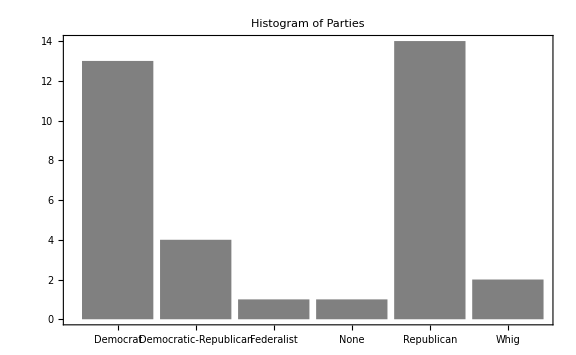

```mathematica
whichparties=histo[listOfPresidents,11,"Histogram of Parties"]
```

## Age

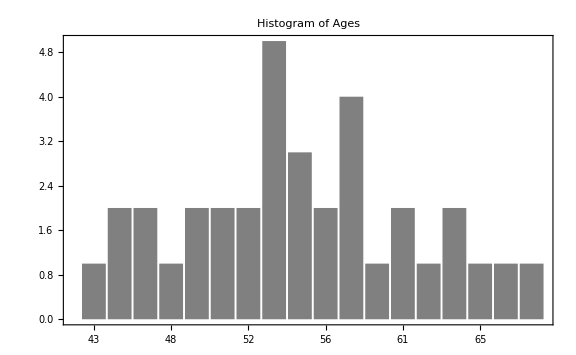

```mathematica
whichages=histo[listOfPresidents,4,"Histogram of Ages"]
```

## Years in Office

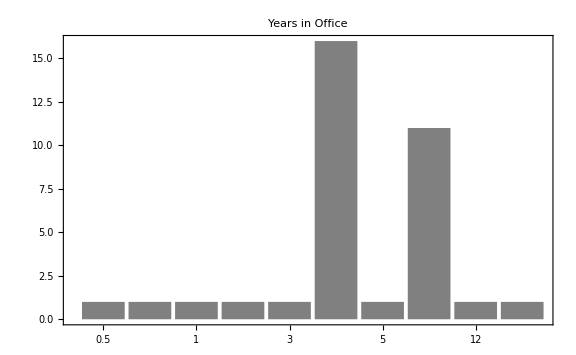

```mathematica
histo[listOfPresidents,2,"Years in Office"]
```

## Which State?

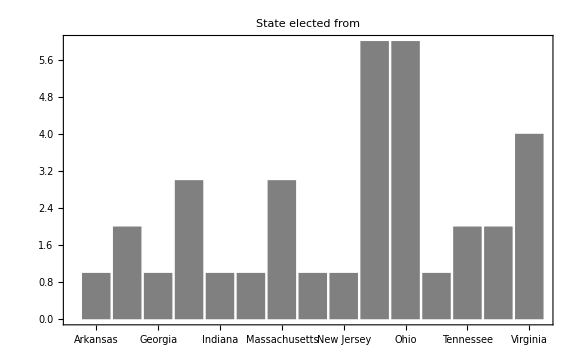

```mathematica
whichstates=histo2[listOfPresidents,5,"State elected from",Large,Pi/4]
```

## Occupation

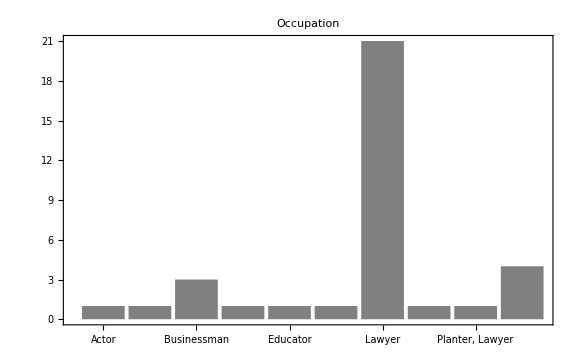

```mathematica
histo[listOfPresidents,12,"Occupation"]
```

## College

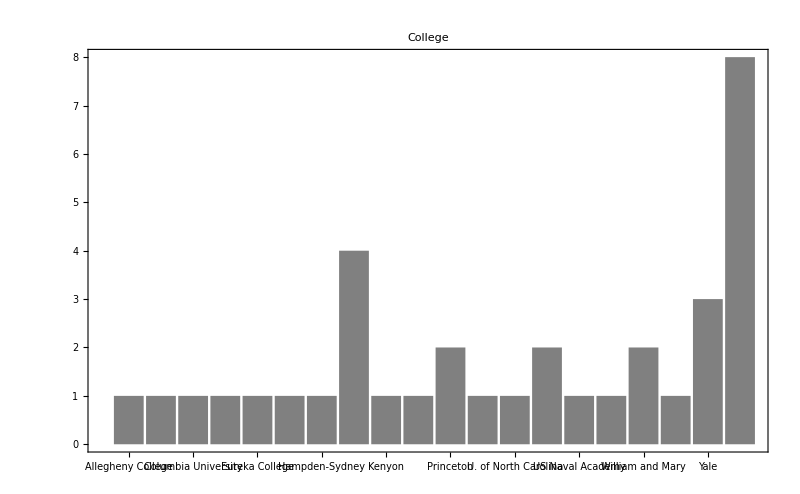

```mathematica
whichcolleges=histo3[listOfPresidents,13,"College",800,3Pi/2]
```

List of Output

```mathematica
listOfFigures={whichparties,whichages,whichstates,whichcollege};
listOfFigureNames={"whichparties","whichages","whichstates","whichcollege"};
```

```mathematica
Table[
Export[ToString[listOfFigureNames[[i]]]<>".png",listOfFigures[[i]]],
{i,1,Length@listOfFigures}]
```

{whichparties.png,whichages.png,whichstates.png,whichcollege.png}

# Some Attempts from Wikipedia List

```mathematica
url="https://en.wikipedia.org/wiki/List_of_Presidents_of_the_United_States#List_of_presidents"
```

https://en.wikipedia.org/wiki/List_of_Presidents_of_the_United_States#List_of_presidents

```mathematica
rawData=Import[url,"XMLObject"];
```

```mathematica
rawHTMLData=Import[url,{"HTML","Source"}];
```

```mathematica
rawHTMLData;
```

```mathematica
wherestarttext="<table class=\"wikitable\" style=\"text-align:center;\">"
whereendtext="<td>57<br />
<small>(<a href=\"/wiki/United_States_presidential_election,_2012\" title=\"United States presidential election, 2012\">2012</a>)</small></td>
</tr>
</table>"
```

<table class="wikitable" style="text-align:center;">

<td>57<br />
<small>(<a href="/wiki/United_States_presidential_election,_2012" title="United States presidential election, 2012">2012</a>)</small></td>
</tr>
</table>

```mathematica
wherestart=StringPosition[rawHTMLData,wherestarttext][[1,1]]
```

30078

```mathematica
whereend=Select[StringPosition[rawHTMLData,whereendtext],#[[1]]>wherestart&][[1,2]]
```

133600

```mathematica
dataCleanLevel1=ImportString[StringTake[rawHTMLData,{wherestart,whereend}],{"html","Data"}];
%//Grid
```

Grid[{Nonpartisan   Federalist   Democratic-Republican   Democratic   Whig   Republican   National Union,{Presidency [a],President,Previous service,Party,Election,Vice President},{1,April 30, 1789 [b] – March 4, 1797,George Washington 1732–1799 (Lived: 67 years) [9] [10] [11],Commander-in-Chief of the Continental Army (1775–1783),Nonpartisan [12],1 ( 1788–89 ),John Adams [c] [d]},2 ( 1792 ),{2,March 4, 1797 – March 4, 1801,John Adams 1735–1826 (Lived: 90 years) [13] [14] [15],1st Vice President of the United States,Federalist,3 ( 1796 ),Thomas Jefferson [e]},{3,March 4, 1801 – March 4, 1809,Thomas Jefferson 1743–1826 (Lived: 83 years) [16] [17] [18],2nd Vice President of the United States,Democratic- Republican,4 ( 1800 ),Aaron Burr March 4, 1801 – March 4, 1805},{5 ( 1804 ),George Clinton March 4, 1805 – March 4, 1809},{4,March 4, 1809 – March 4, 1817,James Madison 1751–1836 (Lived: 85 years) [19] [20] [21],5th United States Secretary of State (1801–1809),Democratic- Republican,6 ( 1808 ),George Clinton March 4, 1809 – April 20, 1812 (Died in office)},Office vacant (Balance of Clinton's term),{7 ( 1812 ),Elbridge Gerry March 4, 1813 – November 23, 1814 (Died in office)},Office vacant (Balance of Gerry's term),{5,March 4, 1817 – March 4, 1825,James Monroe 1758–1831 (Lived: 73 years) [22] [23] [24],7th United States Secretary of State (1811–1817),Democratic- Republican,8 ( 1816 ),Daniel D. Tompkins},9 ( 1820 ),{6,March 4, 1825 – March 4, 1829,John Quincy Adams 1767–1848 (Lived: 80 years) [25] [26] [27],8th United States Secretary of State (1817–1825),Democratic- Republican,10 ( 1824 ),John C. Calhoun},{7,March 4, 1829 – March 4, 1837,Andrew Jackson 1767–1845 (Lived: 78 years) [28] [29] [30],U.S. Senator ( Class 2 ) from Tennessee (1823–1825),Democratic,11 ( 1828 ),John C. Calhoun [f] March 4, 1829 – December 28, 1832 (Resigned from office)},Office vacant (Balance of Calhoun's term),{12 ( 1832 ),Martin Van Buren March 4, 1833 – March 4, 1837},{8,March 4, 1837 – March 4, 1841,Martin Van Buren 1782–1862 (Lived: 79 years) [31] [32] [33],8th Vice President of the United States,Democratic,13 ( 1836 ),Richard Mentor Johnson},{9,March 4, 1841 – April 4, 1841 (Died in office),William Henry Harrison 1773–1841 (Lived: 68 years) [34] [35] [36],United States Minister to Colombia (1828–1829),Whig,14 ( 1840 ),John Tyler (Succeeded to presidency)},{10,April 4, 1841 – March 4, 1845,John Tyler 1790–1862 (Lived: 71 years) [37] [38] [39],10th Vice President of the United States,Whig April 4, 1841 – September 13, 1841,Office vacant},Unaffiliated September 13, 1841 – March 4, 1845 [g],{11,March 4, 1845 – March 4, 1849,James K. Polk 1795–1849 (Lived: 53 years) [40] [41] [42],9th Governor of Tennessee (1839–1841),Democratic,15 ( 1844 ),George M. Dallas},{12,March 4, 1849 – July 9, 1850 (Died in office),Zachary Taylor 1784–1850 (Lived: 65 years) [43] [44] [45],Major General of the 1st Infantry Regiment United States Army (1846–1849),Whig,16 ( 1848 ),Millard Fillmore (Succeeded to presidency)},{13,July 9, 1850 – March 4, 1853,Millard Fillmore 1800–1874 (Lived: 74 years) [46] [47] [48],12th Vice President of the United States,Whig,Office vacant},{14,March 4, 1853 – March 4, 1857,Franklin Pierce 1804–1869 (Lived: 64 years) [49] [50] [51],Brigadier General of the 9th Infantry United States Army (1847–1848),Democratic,17 ( 1852 ),William R. King March 4 – April 18, 1853 (Died in office)},Office vacant (Balance of King's term),{15,March 4, 1857 – March 4, 1861,James Buchanan 1791–1868 (Lived: 77 years) [52] [53] [54],United States Minister to the Court of St James's (1853–1856),Democratic,18 ( 1856 ),John C. Breckinridge},{16,March 4, 1861 – April 15, 1865 ( Died in office ),Abraham Lincoln 1809–1865 (Lived: 56 years) [55] [56] [57],U.S. Representative for Illinois' 7th District (1847–1849),Republican ( National Union ) [h],19 ( 1860 ),Hannibal Hamlin March 4, 1861 – March 4, 1865},{20 ( 1864 ),Andrew Johnson March 4 – April 15, 1865 (Succeeded to presidency)},{17,April 15, 1865 – March 4, 1869,Andrew Johnson 1808–1875 (Lived: 66 years) [58] [59] [60],16th Vice President of the United States,National Union [h] ( Democratic ) [i],Office vacant},{18,March 4, 1869 – March 4, 1877,Ulysses S. Grant 1822–1885 (Lived: 63 years) [61] [62] [63],Commanding General of the U.S. Army (1864–1869),Republican,21 ( 1868 ),Schuyler Colfax March 4, 1869 – March 4, 1873},{22 ( 1872 ),Henry Wilson March 4, 1873 – November 22, 1875 (Died in office)},Office vacant (Balance of Wilson's term),{19,March 4, 1877 – March 4, 1881,Rutherford B. Hayes 1822–1893 (Lived: 70 years) [64] [65] [66],29th & 32nd Governor of Ohio (1868–1872 & 1876–1877),Republican,23 ( 1876 ),William A. Wheeler},{20,March 4, 1881 – September 19, 1881 ( Died in office ),James A. Garfield 1831–1881 (Lived: 49 years) [67] [68] [69],U.S. Representative for Ohio's 19th District (1863–1881),Republican,24 ( 1880 ),Chester A. Arthur (Succeeded to presidency)},{21,September 19, 1881 – March 4, 1885,Chester A. Arthur 1829–1886 (Lived: 57 years) [70] [71] [72],20th Vice President of the United States,Republican,Office vacant},{22,March 4, 1885 – March 4, 1889,Grover Cleveland 1837–1908 (Lived: 71 years) [73] [74],28th Governor of New York (1883–1885),Democratic,25 ( 1884 ),Thomas A. Hendricks March 4 – November 25, 1885 (Died in office)},Office vacant (Balance of Hendricks' term),{23,March 4, 1889 – March 4, 1893,Benjamin Harrison 1833–1901 (Lived: 67 years) [75] [76] [77],U.S. Senator ( Class 1 ) from Indiana (1881–1887),Republican,26 ( 1888 ),Levi P. Morton},{24,March 4, 1893 – March 4, 1897,Grover Cleveland 1837–1908 (Lived: 71 years) [73] [74],22nd President of the United States (1885–1889),Democratic,27 ( 1892 ),Adlai Stevenson},{25,March 4, 1897 – September 14, 1901 ( Died in office ),William McKinley 1843–1901 (Lived: 58 years) [78] [79] [80],39th Governor of Ohio (1892–1896),Republican,28 ( 1896 ),Garret Hobart March 4, 1897 – November 21, 1899 (Died in office)},Office vacant (Balance of Hobart's term),{29 ( 1900 ),Theodore Roosevelt March 4 – September 14, 1901 (Succeeded to presidency)},{26,September 14, 1901 – March 4, 1909,Theodore Roosevelt 1858–1919 (Lived: 60 years) [81] [82] [83],25th Vice President of the United States,Republican,Office vacant September 14, 1901 – March 4, 1905},{30 ( 1904 ),Charles W. Fairbanks March 4, 1905 – March 4, 1909},{27,March 4, 1909 – March 4, 1913,William Howard Taft 1857–1930 (Lived: 72 years) [84] [85] [86],42nd United States Secretary of War (1904–1908),Republican,31 ( 1908 ),James S. Sherman March 4, 1909 – October 30, 1912 (Died in office)},Office vacant (Balance of Sherman's term),{28,March 4, 1913 – March 4, 1921,Woodrow Wilson 1856–1924 (Lived: 67 years) [87] [88] [89],34th Governor of New Jersey (1911–1913),Democratic,32 ( 1912 ),Thomas R. Marshall},33 ( 1916 ),{29,March 4, 1921 – August 2, 1923 (Died in office),Warren G. Harding 1865–1923 (Lived: 57 years) [90] [91] [92],U.S. Senator ( Class 3 ) from Ohio (1915–1921),Republican,34 ( 1920 ),Calvin Coolidge (Succeeded to presidency)},{30,August 2, 1923 – March 4, 1929,Calvin Coolidge 1872–1933 (Lived: 60 years) [93] [94] [95],29th Vice President of the United States,Republican,Office vacant August 2, 1923 – March 4, 1925},{35 ( 1924 ),Charles G. Dawes March 4, 1925 – March 4, 1929},{31,March 4, 1929 – March 4, 1933,Herbert Hoover 1874–1964 (Lived: 90 years) [96] [97] [98],3rd United States Secretary of Commerce (1921–1928),Republican,36 ( 1928 ),Charles Curtis},{32,March 4, 1933 – April 12, 1945 (Died in office),Franklin D. Roosevelt 1882–1945 (Lived: 63 years) [99] [100] [101],44th Governor of New York (1929–1932),Democratic,37 ( 1932 ),John Nance Garner March 4, 1933 – January 20, 1941 [j]},38 ( 1936 ),{39 ( 1940 ),Henry A. Wallace January 20, 1941 – January 20, 1945},{40 ( 1944 ),Harry S. Truman January 20 – April 12, 1945 (Succeeded to presidency)},{33,April 12, 1945 – January 20, 1953,Harry S. Truman 1884–1972 (Lived: 88 years) [102] [103] [104],34th Vice President of the United States,Democratic,Office vacant April 12, 1945 – January 20, 1949},{41 ( 1948 ),Alben W. Barkley January 20, 1949 – January 20, 1953},{34,January 20, 1953 – January 20, 1961,Dwight D. Eisenhower 1890–1969 (Lived: 78 years) [105] [106] [107],Supreme Allied Commander Europe (1949–1952),Republican,42 ( 1952 ),Richard Nixon},43 ( 1956 ),{35,January 20, 1961 – November 22, 1963 ( Died in office ),John F. Kennedy 1917–1963 (Lived: 46 years) [108] [109] [110],U.S. Senator ( Class 1 ) from Massachusetts (1953–1960),Democratic,44 ( 1960 ),Lyndon B. Johnson (Succeeded to presidency)},{36,November 22, 1963 – January 20, 1969,Lyndon B. Johnson 1908–1973 (Lived: 64 years) [111] [112],37th Vice President of the United States,Democratic,Office vacant November 22, 1963 – January 20, 1965},{45 ( 1964 ),Hubert Humphrey January 20, 1965 – January 20, 1969},{37,January 20, 1969 – August 9, 1974 (Resigned from office),Richard Nixon 1913–1994 (Lived: 81 years) [113] [114] [115],36th Vice President of the United States (1953–1961),Republican,46 ( 1968 ),Spiro Agnew January 20, 1969 – October 10, 1973 (Resigned from office)},47 ( 1972 ),Office vacant October 10 – December 6, 1973,Gerald Ford December 6, 1973 – August 9, 1974 (Succeeded to presidency),{38,August 9, 1974 – January 20, 1977,Gerald Ford 1913–2006 (Lived: 93 years) [116] [117] [118],40th Vice President of the United States,Republican,Office vacant August 9 – December 19, 1974},Nelson Rockefeller December 19, 1974 – January 20, 1977,{39,January 20, 1977 – January 20, 1981,Jimmy Carter Born 1924 (92 years old) [119] [120] [121],76th Governor of Georgia (1971–1975),Democratic,48 ( 1976 ),Walter Mondale},{40,January 20, 1981 – January 20, 1989,Ronald Reagan 1911–2004 (Lived: 93 years) [122] [123] [124],33rd Governor of California (1967–1975),Republican,49 ( 1980 ),George H. W. Bush},50 ( 1984 ),{41,January 20, 1989 – January 20, 1993,George H. W. Bush Born 1924 (92 years old) [125] [126] [127],43rd Vice President of the United States,Republican,51 ( 1988 ),Dan Quayle},{42,January 20, 1993 – January 20, 2001,Bill Clinton Born 1946 (70 years old) [128] [129] [130],40th & 42nd Governor of Arkansas (1979–1981 & 1983–1992),Democratic,52 ( 1992 ),Al Gore},53 ( 1996 ),{43,January 20, 2001 – January 20, 2009,George W. Bush Born 1946 (70 years old) [131] [132],46th Governor of Texas (1995–2000),Republican,54 ( 2000 ),Dick Cheney},55 ( 2004 ),{44,January 20, 2009 – Incumbent,Barack Obama Born 1961 (55 years old) [133] [134],U.S. Senator ( Class 3 ) from Illinois (2005–2008),Democratic,56 ( 2008 ),Joe Biden},57 ( 2012 )}]